Инициализация...

Mathematica version is 11.3 Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 11.3 Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.03.001

Release date: 2018/05/05

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.03
BerremanCommonVersion = 6.03
BerremanDirectVersion = 6.03
BerremanInverseVersion = 6.03
FieldAlgebraVersion = 6.03
FieldIOVersion = 6.03
FieldIOFormatVersion = 6.03

Copyright: K^3, 2001 - 2018.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

!!! For absorbing plate I > R + T !!!

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (200 | 800 | 100 | λ | 1/1000000000
0 | 0 | 5 | ϕ | °
0 | 90 | 45 | β | °
0 | 0 | 0.25 | e | )

---------------------------------------------

Оптические параметры толстой пластинки

Для расчетов для различных толщин пластинки нужно поменять значение thickness

Оптические параметры нижней среды...

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,√(epsFuncT.{{1,0,0},{0,1,0},{0,0,1}}),{0,0,30,γ,°},{},,1,1/1000,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},epsFuncT,{{1,0,0},{0,1,0},{0,0,1}},rhoFuncT,Transpose[Conjugate[rhoFuncT]]}},{{200,800,100,λ,1/1000000000},{0,0,5,ϕ,°},{0,90,45,β,°},{0,0,30,γ,°},{0,0,0.25,e},{0,0,1,φ_1,°},{0,0,1,θ_1,°},{0,0,1,ψ_1,°}},{UseThickLastLayer→True}}}

==============================================

Производим вычисления для различных значений параметров....

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.03 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.03 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Uniaxial slightly absorbing thick substrate plate - dispersion calculations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film on a THICK SUBSTRATE plate. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 100 |     Averaging Type:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 3 |     No Of Averaging Points:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |     Averaging Periods:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | √(epsFuncT.{{1,0,0},{0,1,0},{0,0,1}}) |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | ^2 Attributes[eps$132581] = {Temporary}
 
eps$132581 = epsFuncT
 
epsFuncT[lambda_] := Module[{nVal1, nVal2, nVal3, epsRet}, nVal1 = refrIndex$La3Ga5SiO14$Ordinary[lambda]; nVal2 = refrIndex$La3Ga5SiO14$Ordinary[lambda]; nVal3 = refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda]; epsRet = EpsilonFromN[nVal1, nVal2, nVal3]; Return[N[epsRet]]; ]
 
                                1
lambda = {200, 800, 100, λ, ----------}
                            1000000000
 
                                                                                    0.5
refrIndex$La3Ga5SiO14$Ordinary[lambda_] := refrIndex[lambda, 2.49811, 0.129788 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                      4
                                                                                    10
 
refrIndex[lambda_, kCoeff_, lambdaNull_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := Sqrt[refrIndexSquared[lambda, kCoeff, lambdaNull]] + I absorptionCoeff[lambda, kAbsorption, lambdaMidPoint, lambdaHalfWidth]
 
                                                                       2
                                                          kCoeff lambda
refrIndexSquared[lambda_, kCoeff_, lambdaNull_] := 1 + ---------------------
                                                             2             2
                                                       lambda  - lambdaNull
 
                                                                                                                                   2
                                                                                                          (lambda - lambdaMidPoint)
absorptionCoeff[lambda_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := kAbsorption Exp[-(-------------------------------------------------)]
                                                                                                                                               2
                                                                                               sigmaAbsorption[lambdaMidPoint, lambdaHalfWidth]
 
                                                      lambdaHalfWidth - lambdaMidPoint
sigmaAbsorption[lambdaMidPoint_, lambdaHalfWidth_] := --------------------------------
                                                                   Log[2]
 
         1
mkm = -------
      1000000
 
                                                                                         1.
refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda_] := refrIndex[lambda, 2.54081, 0.129148 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                           4
                                                                                         10
 
                                                   2               2               2
EpsilonFromN[n1_] := Module[{retval}, retval = {{n1 , 0, 0}, {0, n1 , 0}, {0, 0, n1 }}; Return[retval]; ]
 
                                                             2               2               2
EpsilonFromN[n1_, n2_, n3_] := Module[{retval}, retval = {{n1 , 0, 0}, {0, n2 , 0}, {0, 0, n3 }}; Return[retval]; ] | 0 | 0 |  |  | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | ^2 Attributes[ro$132581] = {Temporary}
 
ro$132581 = rhoFuncT
 
rhoFuncT[lambda_] := Module[{nVal1, nVal2, nVal3, rhoRet}, rhoRet = DiagonalMatrix[{g11$La3Ga5SiO14[lambda], 0, g33$La3Ga5SiO14[lambda]}]; Return[N[rhoRet]]; ]
 
                                1
lambda = {200, 800, 100, λ, ----------}
                            1000000000
 
                                                                                  0.6106  0.6278
g11$La3Ga5SiO14[lambda_] := gyration11Func[lambda, refrIndex$La3Ga5SiO14$Average, ------, ------, 0.156 mkm]
                                                                                     11      11
                                                                                   10      10
 
                                                                                                                                                                      2
                                                                                                                                 a2Coeff                a3Coeff lambda
gyration11Func[lambda_, refrIndAverageFunc_, a2Coeff_, a3Coeff_, lambda2Coeff_] := I (lambda refrIndAverageFunc[lambda] (----------------------- + --------------------------))
                                                                                                                               2               2          2               2 2
                                                                                                                         lambda  - lambda2Coeff    (lambda  - lambda2Coeff )
 
                                          Re[refrIndex$La3Ga5SiO14$Ordinary[lambda]] + Re[refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda]]
refrIndex$La3Ga5SiO14$Average[lambda_] := --------------------------------------------------------------------------------------------
                                                                                       2
 
                                                                                    0.5
refrIndex$La3Ga5SiO14$Ordinary[lambda_] := refrIndex[lambda, 2.49811, 0.129788 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                      4
                                                                                    10
 
refrIndex[lambda_, kCoeff_, lambdaNull_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := Sqrt[refrIndexSquared[lambda, kCoeff, lambdaNull]] + I absorptionCoeff[lambda, kAbsorption, lambdaMidPoint, lambdaHalfWidth]
 
                                                                       2
                                                          kCoeff lambda
refrIndexSquared[lambda_, kCoeff_, lambdaNull_] := 1 + ---------------------
                                                             2             2
                                                       lambda  - lambdaNull
 
                                                                                                                                   2
                                                                                                          (lambda - lambdaMidPoint)
absorptionCoeff[lambda_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := kAbsorption Exp[-(-------------------------------------------------)]
                                                                                                                                               2
                                                                                               sigmaAbsorption[lambdaMidPoint, lambdaHalfWidth]
 
                                                      lambdaHalfWidth - lambdaMidPoint
sigmaAbsorption[lambdaMidPoint_, lambdaHalfWidth_] := --------------------------------
                                                                   Log[2]
 
         1
mkm = -------
      1000000
 
                                                                                         1.
refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda_] := refrIndex[lambda, 2.54081, 0.129148 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                           4
                                                                                         10
 
                                                                                  0.6072
g33$La3Ga5SiO14[lambda_] := gyration33Func[lambda, refrIndex$La3Ga5SiO14$Average, ------, 0.198 mkm]
                                                                                     11
                                                                                   10
 
                                                                           lambda refrIndAverageFunc[lambda] a1Coeff
gyration33Func[lambda_, refrIndAverageFunc_, a1Coeff_, lambda1Coeff_] := I -----------------------------------------
                                                                                          2               2
                                                                                    lambda  - lambda1Coeff | 0 | 0 |  |  | 0 | 0 |  | ^2 Attributes[roT$132581] = {Temporary}
 
roT$132581 = rhoFuncT
 
rhoFuncT[lambda_] := Module[{nVal1, nVal2, nVal3, rhoRet}, rhoRet = DiagonalMatrix[{g11$La3Ga5SiO14[lambda], 0, g33$La3Ga5SiO14[lambda]}]; Return[N[rhoRet]]; ]
 
                                1
lambda = {200, 800, 100, λ, ----------}
                            1000000000
 
                                                                                  0.6106  0.6278
g11$La3Ga5SiO14[lambda_] := gyration11Func[lambda, refrIndex$La3Ga5SiO14$Average, ------, ------, 0.156 mkm]
                                                                                     11      11
                                                                                   10      10
 
                                                                                                                                                                      2
                                                                                                                                 a2Coeff                a3Coeff lambda
gyration11Func[lambda_, refrIndAverageFunc_, a2Coeff_, a3Coeff_, lambda2Coeff_] := I (lambda refrIndAverageFunc[lambda] (----------------------- + --------------------------))
                                                                                                                               2               2          2               2 2
                                                                                                                         lambda  - lambda2Coeff    (lambda  - lambda2Coeff )
 
                                          Re[refrIndex$La3Ga5SiO14$Ordinary[lambda]] + Re[refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda]]
refrIndex$La3Ga5SiO14$Average[lambda_] := --------------------------------------------------------------------------------------------
                                                                                       2
 
                                                                                    0.5
refrIndex$La3Ga5SiO14$Ordinary[lambda_] := refrIndex[lambda, 2.49811, 0.129788 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                      4
                                                                                    10
 
refrIndex[lambda_, kCoeff_, lambdaNull_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := Sqrt[refrIndexSquared[lambda, kCoeff, lambdaNull]] + I absorptionCoeff[lambda, kAbsorption, lambdaMidPoint, lambdaHalfWidth]
 
                                                                       2
                                                          kCoeff lambda
refrIndexSquared[lambda_, kCoeff_, lambdaNull_] := 1 + ---------------------
                                                             2             2
                                                       lambda  - lambdaNull
 
                                                                                                                                   2
                                                                                                          (lambda - lambdaMidPoint)
absorptionCoeff[lambda_, kAbsorption_, lambdaMidPoint_, lambdaHalfWidth_] := kAbsorption Exp[-(-------------------------------------------------)]
                                                                                                                                               2
                                                                                               sigmaAbsorption[lambdaMidPoint, lambdaHalfWidth]
 
                                                      lambdaHalfWidth - lambdaMidPoint
sigmaAbsorption[lambdaMidPoint_, lambdaHalfWidth_] := --------------------------------
                                                                   Log[2]
 
         1
mkm = -------
      1000000
 
                                                                                         1.
refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda_] := refrIndex[lambda, 2.54081, 0.129148 mkm, ---, 0.28 mkm, 0.3 mkm]
                                                                                           4
                                                                                         10
 
                                                                                  0.6072
g33$La3Ga5SiO14[lambda_] := gyration33Func[lambda, refrIndex$La3Ga5SiO14$Average, ------, 0.198 mkm]
                                                                                     11
                                                                                   10
 
                                                                           lambda refrIndAverageFunc[lambda] a1Coeff
gyration33Func[lambda_, refrIndAverageFunc_, a1Coeff_, lambda1Coeff_] := I -----------------------------------------
                                                                                          2               2
                                                                                    lambda  - lambda1Coeff | 0 | 0 |  |  | 0 | 0 | 
 | 0 |  | 0 |  | 0 |  | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0 |  | 0 | 
 | 0 | 0 |  |  | 0 | 0 |  |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 |  |  | 0 | 0 |  |  | 0 | 0 |  |  | 0 | 0 |  | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ_1 | θ_1 | ψ_1 | Output | Layer 1: Re[Eps[x,x]] | Layer 1: Re[Eps[y,y]] | Layer 1: Re[Eps[z,z]] | S_(R,0) | S_(R,1) | S_(R,2) | S_(R,3) | R | T | γ_R | ° γ_R | χ_R | ° χ_R | p_R | χ_r | e_r | ψ_pp | Δ_pp | R_p | R_s | T_p | T_s
 | 1. | 200. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 5.31546 | 5.31546 | 5.35801 | 0.269541 | 0.269541 | 8.11923×10^-10 | 0.0000288347 | 0.269541 | 0.729008 | 0.0000534886 | 0.00306467 | 0.785384 | 44.9992 | 1. | 8.53774×10^-7 | 0.00015131 | 45. | -180. | 0.269541 | 4.46212×10^-9 | 0.330495 | 0.398513
 | 2. | 200. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 5.31546 | 5.31546 | 5.35801 | 0.269541 | -3.86923×10^-10 | -0.269541 | 0.0000480232 | 0.269541 | 0.729008 | 0.0000890834 | 0.0051041 | 1.57071 | 89.9949 | 1. | -45. | 0. | 45. | -180. | 0.13477 | 0.13477 | 0.727418 | 0.00159003
 | 3. | 200. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 5.31546 | 5.31546 | 5.35801 | 0.269541 | -0.269541 | 9.11949×10^-9 | -0.0000288347 | 0.269541 | 0.729008 | -0.0000534886 | -0.00306467 | -0.78524 | -44.9909 | 1. | 90. | -0.00015131 | 45. | -180. | 4.46212×10^-9 | 0.269541 | 0.398513 | 0.330495
 | 4. | 300. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 4.07334 | 4.07334 | 4.1188 | 0.120522 | 0.120522 | 3.79301×10^-10 | 9.2063×10^-6 | 0.120522 | 0.215224 | 0.0000381936 | 0.00218833 | 0.785378 | 44.9988 | 1. | 0. | 0.0000442588 | 45. | -179.999 | 0.120522 | 2.51128×10^-10 | 0.00457851 | 0.210645
 | 5. | 300. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 4.07334 | 4.07334 | 4.1188 | 0.120522 | -2.94473×10^-10 | -0.120522 | 2.15539×10^-7 | 0.120522 | 0.215224 | 8.94193×10^-7 | 0.0000512335 | 1.5708 | 89.9999 | 1. | -45. | 0. | 45. | -179.999 | 0.0602608 | 0.0602608 | 0.138667 | 0.0765564
 | 6. | 300. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 4.07334 | 4.07334 | 4.1188 | 0.120522 | -0.120522 | 4.07253×10^-10 | -9.2063×10^-6 | 0.120522 | 0.215224 | -0.0000381936 | -0.00218833 | -0.785376 | -44.9987 | 1. | 90. | -0.0000442588 | 45. | -179.999 | 2.51128×10^-10 | 0.120522 | 0.210645 | 0.00457851
 | 7. | 400. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 3.79206 | 3.79206 | 3.8365 | 0.187272 | 0.187272 | 1.14961×10^-10 | 6.60556×10^-6 | 0.187272 | 0.812727 | 0.0000176363 | 0.00101049 | 0.785389 | 44.9995 | 1. | 8.53774×10^-7 | 0.0000278635 | 45. | -180. | 0.187272 | 0. | 0.545235 | 0.267492
 | 8. | 400. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 3.79206 | 3.79206 | 3.8365 | 0.187272 | -1.52881×10^-10 | -0.187272 | 5.46885×10^-6 | 0.187272 | 0.812727 | 0.0000146014 | 0.000836598 | 1.57078 | 89.9992 | 1. | -45. | 0. | 45. | -180. | 0.0936359 | 0.0936359 | 0.788262 | 0.0244655
 | 9. | 400. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 3.79206 | 3.79206 | 3.8365 | 0.187272 | -0.187272 | 0. | -6.60556×10^-6 | 0.187272 | 0.812727 | -0.0000176363 | -0.00101049 | -0.785393 | -44.9997 | 1. | 90. | -0.0000278635 | 45. | -180. | 0. | 0.187272 | 0.267492 | 0.545235
 | 10. | 500. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 3.67859 | 3.67859 | 3.72245 | 0.18011 | 0.18011 | 0. | 6.51069×10^-6 | 0.18011 | 0.819889 | 0.0000180742 | 0.00103558 | 0.785393 | 44.9997 | 1. | 0. | 0.000020783 | 45. | -180. | 0.18011 | 0. | 0.723604 | 0.0962853
 | 11. | 500. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 3.67859 | 3.67859 | 3.72245 | 0.18011 | -1.26669×10^-10 | -0.18011 | 2.67491×10^-6 | 0.18011 | 0.819889 | 7.42577×10^-6 | 0.000425465 | 1.57079 | 89.9996 | 1. | -45. | 0. | 45. | -180. | 0.0900549 | 0.0900549 | 0.6739 | 0.145989
 | 12. | 500. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 3.67859 | 3.67859 | 3.72245 | 0.18011 | -0.18011 | 0. | -6.51069×10^-6 | 0.18011 | 0.819889 | -0.0000180742 | -0.00103558 | -0.785399 | -45. | 1. | 90. | -0.000020783 | 45. | -180. | 0. | 0.18011 | 0.0962853 | 0.723604
 | 13. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 3.62074 | 3.62074 | 3.66425 | 0.176398 | 0.176398 | 0. | 5.55897×10^-6 | 0.176398 | 0.823601 | 0.0000157569 | 0.000902801 | 0.785395 | 44.9998 | 1. | 8.53774×10^-7 | 0.0000167131 | 45. | -180. | 0.176398 | 0. | 0.781036 | 0.0425645
 | 14. | 600. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 3.62074 | 3.62074 | 3.66425 | 0.176398 | 0. | -0.176398 | 1.44513×10^-6 | 0.176398 | 0.823601 | 4.0962×10^-6 | 0.000234695 | 1.57079 | 89.9998 | 1. | -45. | 0. | 45. | -180. | 0.0881991 | 0.0881991 | 0.594131 | 0.22947
 | 15. | 600. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 3.62074 | 3.62074 | 3.66425 | 0.176398 | -0.176398 | 0. | -5.55897×10^-6 | 0.176398 | 0.823601 | -0.0000157569 | -0.000902801 | -0.785399 | -45. | 1. | 90. | -0.0000167131 | 45. | -180. | 0. | 0.176398 | 0.0425645 | 0.781036
 | 16. | 700. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 3.58705 | 3.58705 | 3.63035 | 0.174218 | 0.174218 | 0. | 4.74697×10^-6 | 0.174218 | 0.825781 | 0.0000136237 | 0.000780578 | 0.785396 | 44.9999 | 1. | 0. | 0.0000140317 | 45. | -180. | 0.174218 | 0. | 0.804057 | 0.0217247
 | 17. | 700. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 3.58705 | 3.58705 | 3.63035 | 0.174218 | 0. | -0.174218 | 8.65052×10^-7 | 0.174218 | 0.825781 | 2.48267×10^-6 | 0.000142247 | 1.57079 | 89.9999 | 1. | -45. | 0. | 45. | -180. | 0.087109 | 0.087109 | 0.545057 | 0.280724
 | 18. | 700. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 3.58705 | 3.58705 | 3.63035 | 0.174218 | -0.174218 | 0. | -4.74697×10^-6 | 0.174218 | 0.825781 | -0.0000136237 | -0.000780578 | -0.785399 | -45. | 1. | 90. | -0.0000140317 | 45. | -180. | 0. | 0.174218 | 0.0217247 | 0.804057
 | 19. | 800. | 0. | 0. | 0. | 0. | 0. | 0. | 0. |  | 3.56564 | 3.56564 | 3.6088 | 0.172825 | 0.172825 | 0. | 4.11975×10^-6 | 0.172825 | 0.827174 | 0.0000119188 | 0.000682897 | 0.785397 | 44.9999 | 1. | 0. | 0.0000121173 | 45. | -180. | 0.172825 | 0. | 0.814906 | 0.0122676
 | 20. | 800. | 0. | 45. | 0. | 0. | 0. | 0. | 0. |  | 3.56564 | 3.56564 | 3.6088 | 0.172825 | 0. | -0.172825 | 5.59154×10^-7 | 0.172825 | 0.827174 | 1.61769×10^-6 | 0.0000926865 | 1.57079 | 89.9999 | 1. | -45. | 0. | 45. | -180. | 0.0864127 | 0.0864127 | 0.513572 | 0.313602
 | 21. | 800. | 0. | 90. | 0. | 0. | 0. | 0. | 0. |  | 3.56564 | 3.56564 | 3.6088 | 0.172825 | -0.172825 | 0. | -4.11975×10^-6 | 0.172825 | 0.827174 | -0.0000119188 | -0.000682897 | -0.785398 | -45. | 1. | 90. | -0.0000121173 | 45. | -180. | 0. | 0.172825 | 0.0122676 | 0.814906)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Sun 13 May 2018 11:33:45, time used: 13.454, total time used: 13.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Component of Matrix Epsilon.

-Graphics3D-

==============================================

Component of Matrix Epsilon.

-Graphics3D-

==============================================

Component of Matrix Epsilon.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

γ of Stokes Vector R.

-Graphics3D-

==============================================

γ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

χ of Stokes Vector R.

-Graphics3D-

==============================================

χ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

p of Stokes Vector R.

-Graphics3D-

==============================================

Azimuth of Reflected light in Degrees (new).

-Graphics3D-

==============================================

Ellipticity of Reflected light (new).

-Graphics3D-

==============================================

Psi pp in degrees.

-Graphics3D-

==============================================

Delta pp in degrees.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Component of Matrix Epsilon.

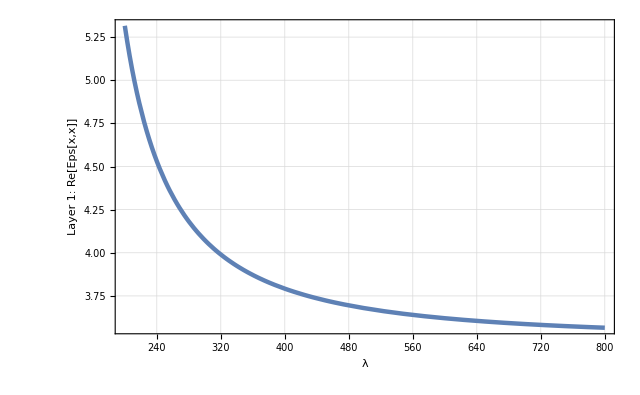

{Component of Matrix Epsilon.,Component of Matrix Epsilon.}

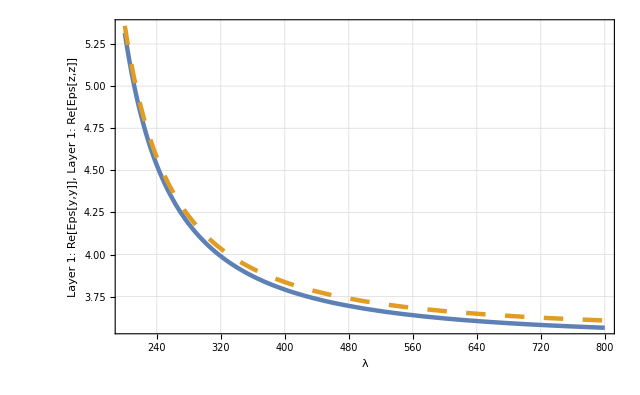

Stokes Vector R.

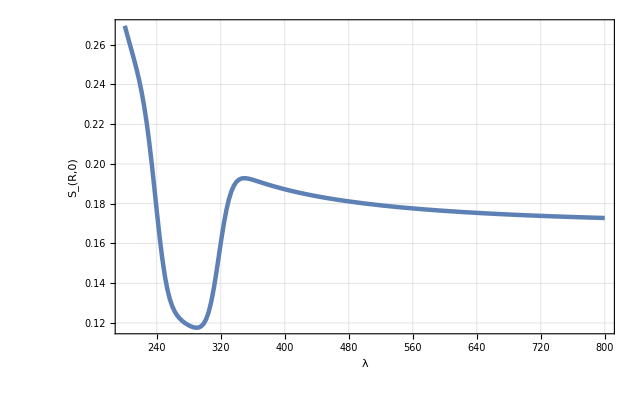

Stokes Vector R.

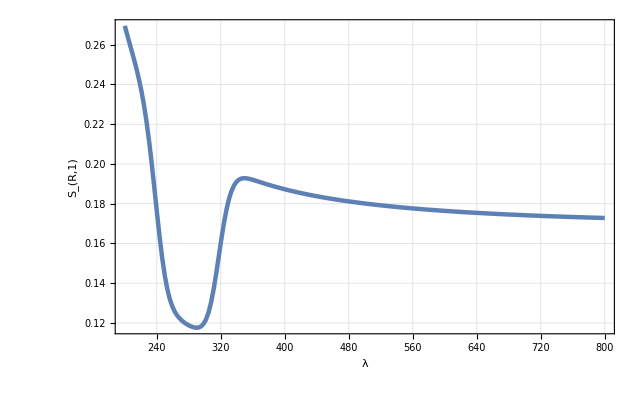

Stokes Vector R.

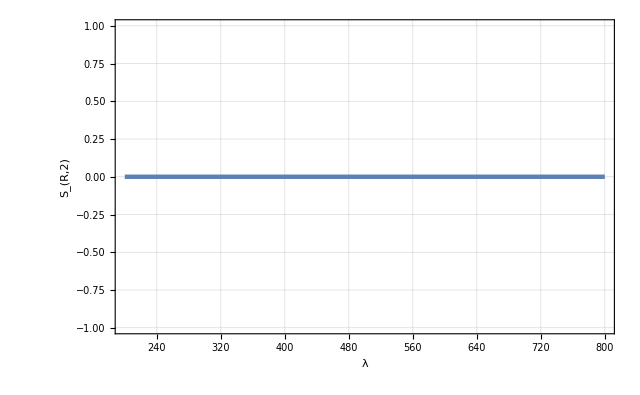

Stokes Vector R.

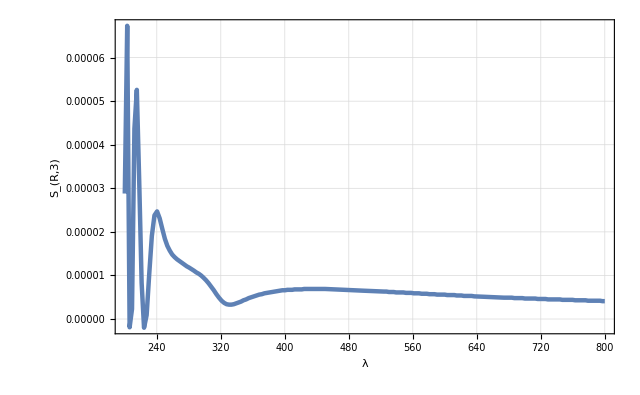

Full intensity of Reflected light.

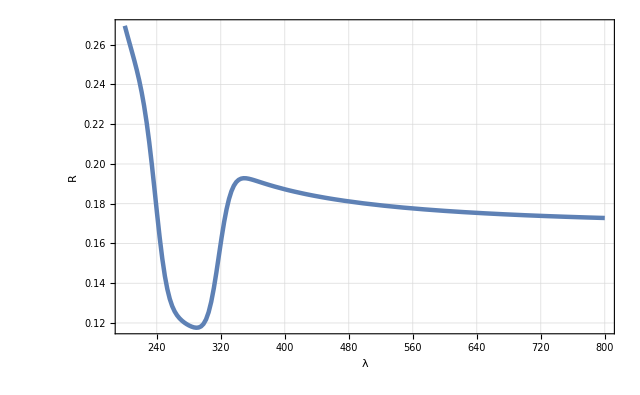

Full intensity of Transmitted light.

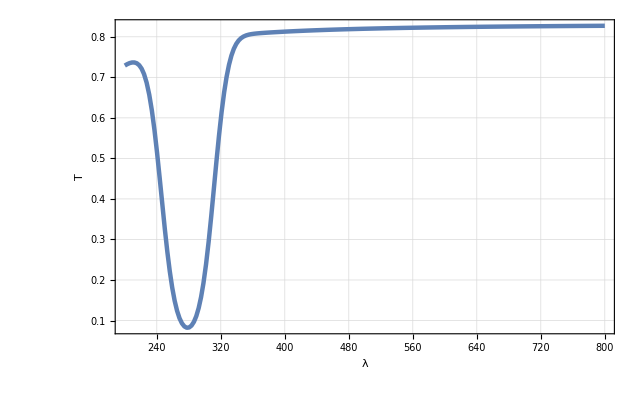

γ of Stokes Vector R.

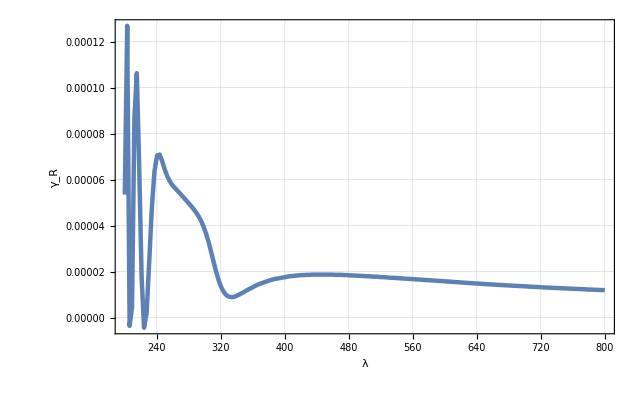

γ of Stokes Vector R (in degrees).

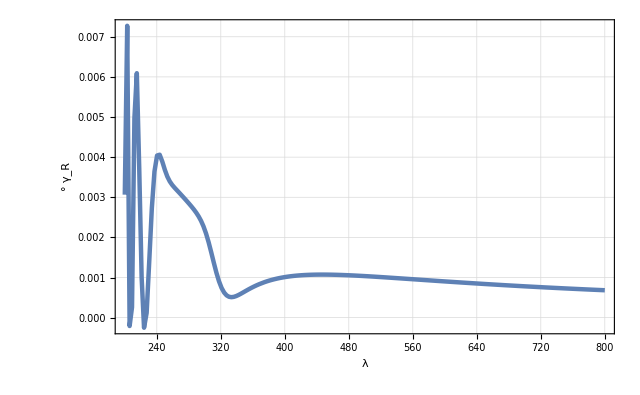

χ of Stokes Vector R.

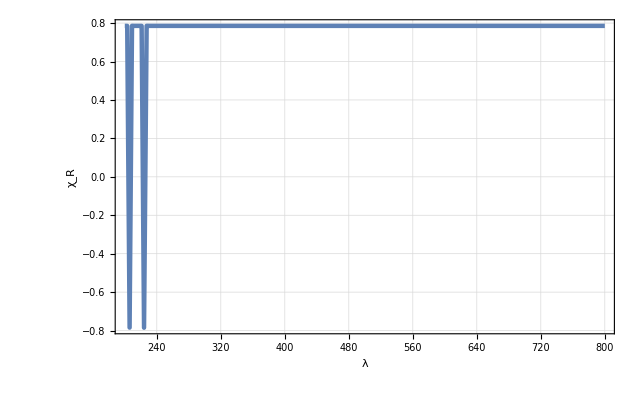

χ of Stokes Vector R (in degrees).

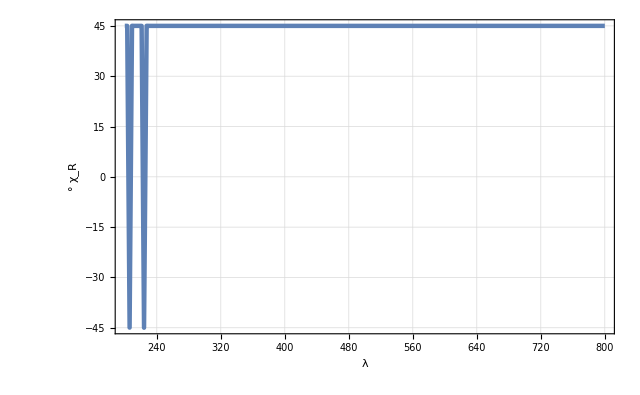

p of Stokes Vector R.

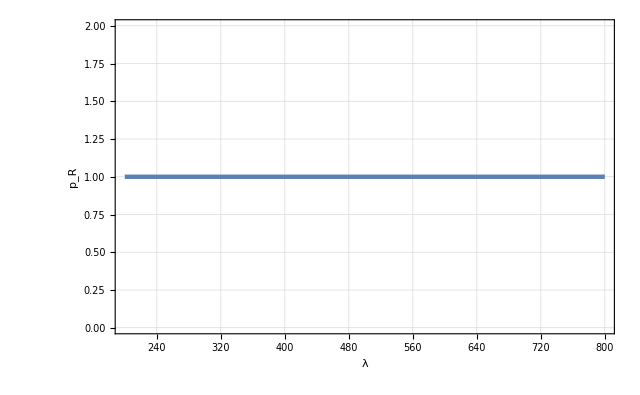

Azimuth of Reflected light in Degrees (new).

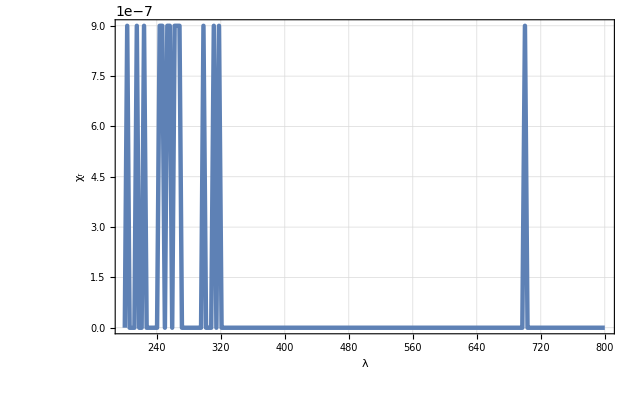

Ellipticity of Reflected light (new).

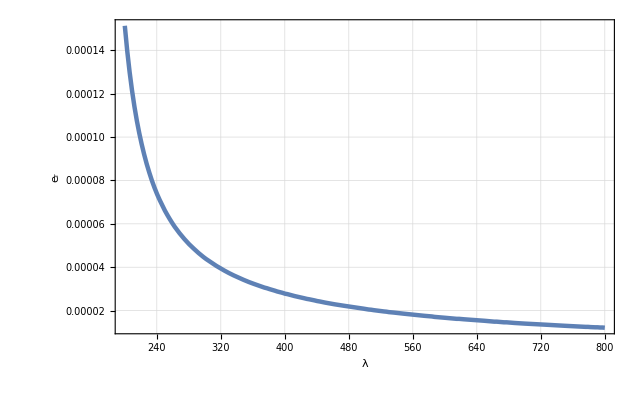

Psi pp in degrees.

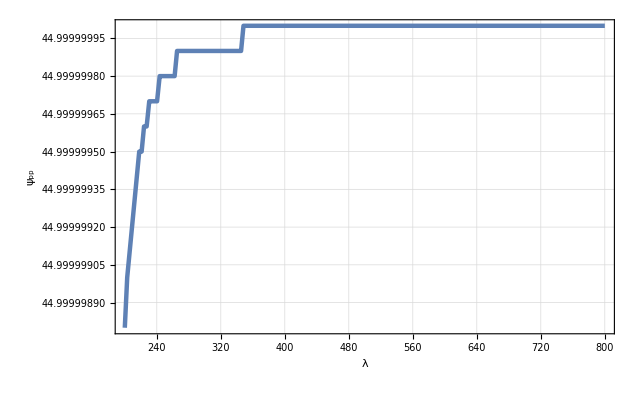

Delta pp in degrees.

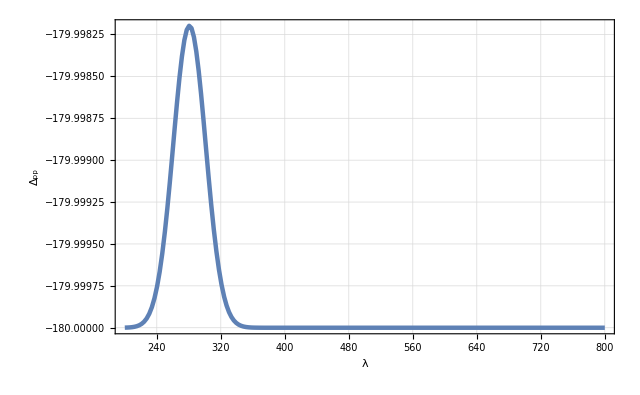

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

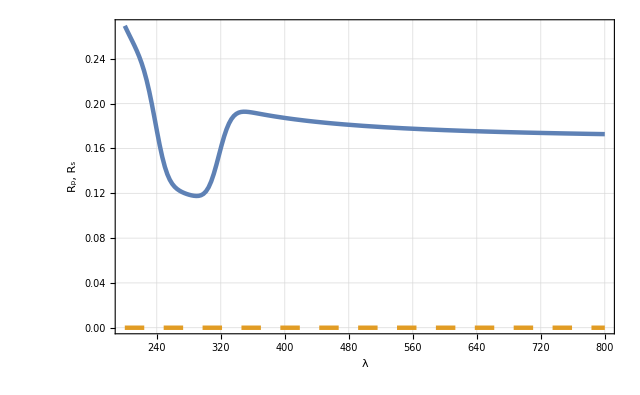

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

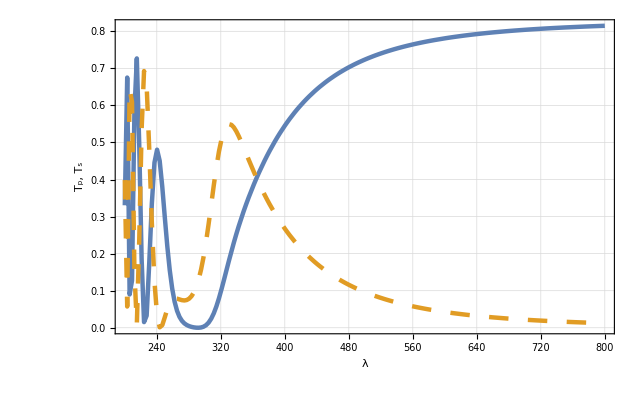

Sun 13 May 2018 11:49:46, time used: 961, total time used: 975.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
BaseDir = "C:\\GitHub\\BM\\";
PathList = {BaseDir <> "Kernel\\"};
OutDir = BaseDir <> "Calc\\";
(* ============================================== *)
BaseFileName = "Example_09";
(* ============================================== *)
useParallelTbl = False;
Get["BerremanInit.m", Path -> PathList];
InitializeBM[PathList, useParallelTbl];
(* ============================================== *)
opts =
    {
      BDPlotFigures -> True,
      UseEulerAngles -> False,
      NoOfAveragingPoints -> 3
    };
(* ============================================== *)

FuncList =
    {
      EpsComponent[1, 1, 1, 1],
      {EpsComponent[1, 1, 2, 2], EpsComponent[1, 1, 3, 3]},
      StokesVectorR[1],
      StokesVectorR[2],
      StokesVectorR[3],
      StokesVectorR[4],
      RFull,
      TFull,
      StokesGammaR,
      StokesGammaDegreeR,
      StokesChiR,
      StokesChiDegreeR,
      StokesPolarizedR,
      XirDegree,
      Elr,
      PsiPPDegree,
      DeltaPPDegree,
      {Rx, Ry},
      {Tx, Ty}
    };
(* ============================================== *)
systemDescription = "Uniaxial slightly absorbing thick substrate plate - dispersion calculations.";
Print["!!! For absorbing plate I > R + T !!!"];
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper = 1;

lambda = {200, 800, 100, "λ", nm};
fita = {0, 0, 5, "ϕ", Degree};
beta = {0, 90, 45, "β", Degree};
gamma = {0, 0, 30, "γ", Degree};
ellipt = {0, 0, 0.25, "e"};
fi = {0, 0, 1, "φ", Degree};

incidentLight = CreateIncidentRay[nUpper, lambda, fita, beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры толстой пластинки"];
Print["Для расчетов для различных толщин пластинки нужно поменять значение thickness"];
thickness = 1 mm;

epsFuncT[lambda_] := Module[{nVal1, nVal2, nVal3, epsRet},
  nVal1 = refrIndex$La3Ga5SiO14$Ordinary[lambda];
  nVal2 = refrIndex$La3Ga5SiO14$Ordinary[lambda];
  nVal3 = refrIndex$La3Ga5SiO14$ExtraOrdinary[lambda];
  epsRet = EpsilonFromN[nVal1, nVal2, nVal3];
  Return[N[epsRet]];
];

muT := DiagonalMatrix[{1, 1, 1}];

rhoFuncT[lambda_] := Module[{nVal1, nVal2, nVal3, rhoRet},
  rhoRet = DiagonalMatrix[{g11$La3Ga5SiO14[lambda], 0, g33$La3Ga5SiO14[lambda]}];
  Return[N[rhoRet]];
];

fiThickPlate = {0, 0, 30, Subscript["φ", "t"], Degree};
thetaThickPlate = {0, 0, 30, Subscript["θ", "t"], Degree};
psiThickPlate = {0, 0, 30, Subscript["ψ", "t"], Degree};
rotationAnglesThickPlate = {fiThickPlate, thetaThickPlate, psiThickPlate};

thickPlate = CreateThickPlate[thickness, rotationAnglesThickPlate, epsFuncT, muT, rhoFuncT];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
nLower = 1;
lowerMedia = CreateSemiInfiniteMediaFromN[nLower];
(* ============================================== *)
If[useParallelTbl == True,
  Print["Distributing definitions for parallel calculations..."];
  DistributeDefinitions[epsFunc1, epsFuncT];
];
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight, gamma, thickPlate, lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc = PerformAllCalculations[layeredSystem, FuncList, systemDescription, opts];
(* ============================================== *)
```